# First Pass at Interpolation with Mathematica.

In this lab we’ll be looking at tables of data, displaying scatter-plots, and using the built in Interpolation function.

## X-Y data tables

We’ve looked at lists before, but to define a list of coordinates, we make a list of lists, each sublist of length 2:

```mathematica
Clear[data1];
data1={{0,1}, {0.25,0.5},{0.5, -2},
{0.75,1},{1,3},{1.25, 3},{1.5, 2}, 
{1.75,0},{2, -1}}
```

{{0,1},{0.25,0.5},{0.5,-2},{0.75,1},{1,3},{1.25,3},{1.5,2},{1.75,0},{2,-1}}

## Looking at data tables

We can use MatrixForm to get a better look at our table:

```mathematica
MatrixForm[data1]
```

(0 | 1
0.25 | 0.5
0.5 | -2
0.75 | 1
1 | 3
1.25 | 3
1.5 | 2
1.75 | 0
2 | -1)

```mathematica
Length[data1]
```

9

## Visualizing Scatter-plots

Mathematica comes with a ListPlot[] function for this very purpose:

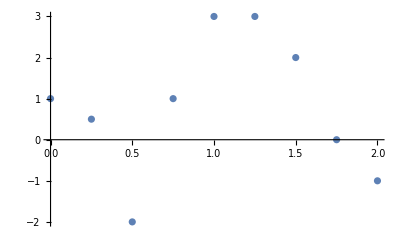

```mathematica
dots1 = ListPlot[data1]
```

## The Interpolating Polynomial

Lets feed the data into the function and see how the polynomial is displayed:

```mathematica
Clear[g];
g[x_] = InterpolatingPolynomial[data1, x]
```

-1+(-2+x) (-1+(-3+(-12.6667+(11.5048+(28.7492+(-24.5841+(54.4508-29.2571 (-0.75+x)) (-1.5+x)) (-0.25+x)) (-1.75+x)) (-0.5+x)) (-1+x)) x)

```mathematica
Expand[g[x]]
```

1+79.3619 x-673.654 x^2+1987.82 x^3-2911.38 x^4+2388.62 x^5-1120.71 x^6+281.194 x^7-29.2571 x^8

## Graphing

We already know how to plot functions:

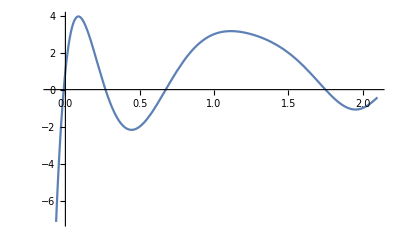

```mathematica
g1 = Plot[g[x], {x, -0.1, 2.1}]
```

Let’s use Show[] to get the dots and the function on the same display

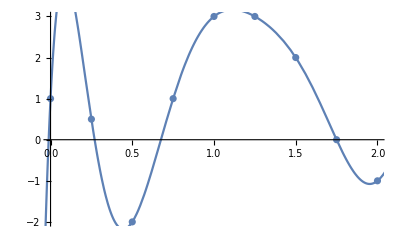

```mathematica
Show[dots1, g1]
```

## Modeling a given function

Let’s try to get a 10th degree polynomial to model the behaviour of f(x)= 1/(1+25 x^2) on the interval [-1,1]

## Your Turn!

Exercise 1: Find the interpolating polynomial for the points: (1,2),(2,48),(3,272),(-4,1182),(5,2262) and evaluate the polynomial at x=-1(you should get 12).

Exercise 2:  Make a data set of 11 evenly spaced points of the function f(x)=arctan(x)on the interval [1,6]. FInd a 10th degree polynomial that interpolates the data. Finally, make a data set of the difference between f(x) and the polynomial on 33 equally spaced points in the interval [0,8]. Learn a valuable lesson...